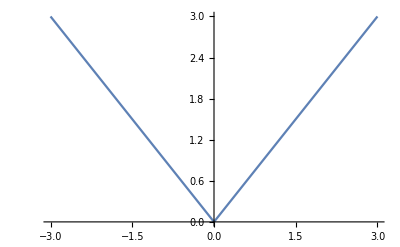

```mathematica
gap[x_]:=Piecewise[{{-x,x<0},{x,x>0}}]
Plot[gap[x],{x,-3,3}]
```

```mathematica
hun = {1,2,3}
```

{1,2,3}

```mathematica
gap[hun]
```

Piecewise[{{{-1,-2,-3}, {1,2,3}<0}, {{1,2,3}, {1,2,3}>0}, {0, True}}]

```mathematica
Attributes[gap]
```

{}

```mathematica
eg[x_]:=x^2
```

```mathematica
Attributes[eg]
```

{}

```mathematica
eg[hun]
```

{1,4,9}

```mathematica
Attributes[Power]
```

{Listable,NumericFunction,OneIdentity,Protected}

```mathematica
AbsoluteTiming[Do[Power[3,100],100000]]
```

{0.151558,Null}

```mathematica
AbsoluteTiming[Do[3^100,100000]]
```

{0.162099,Null}

```mathematica
num=50;
candmoves=Developer`ToPackedArray[{-eps,0.,eps}];
xInit=ConstantArray[0.,{nn}];


f1[x_]:=Piecewise[{{-3*x,x<0},{-x^3*(1/2)^2/24+x,x>0}}]
f[x_]:=With [{ciccio = UnitStep[x]}, ciccio*(-x^3*(1/2)^2/24+x)+Subtract[1,ciccio]*-5*x]
g[x_]:=(x^2-1)*x^2
```

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0.,{nn}].

```mathematica
min=0;
time=0;
metaTime=ConstantArray[0,{nn}];
xOld=xInit;
(*enOld=With[{square=xOld xOld},((1/2)*square-1.)*(1/2) square];*)
enOld = f[xOld];
{{AbsoluteTiming[While[min==0,xNew=RandomChoice[candmoves,nn]+xOld;
enNew=f[xNew];
alfas=Exp[tmp Ramp[Subtract[enNew,enOld]]];
betas=RandomReal[{0.,1.},nn];
xOld=With[{λ=UnitStep[Subtract[alfas,betas]]},λ xNew+Subtract[1,λ] xOld];
enOld=With[{λ=UnitStep[Subtract[alfas,betas]]},λ enNew+Subtract[1,λ] enOld];
metaTime=With[{λ=UnitStep[-xOld+6],μ=Unitize[metaTime]},Subtract[1,λ] (μ metaTime+Subtract[1,μ] time)+λ metaTime];
min=Min[metaTime];
++time];]}, {□}}
```

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0,{nn}].

RandomChoice::array: The array dimensions nn given in position 2 of RandomChoice[{-eps,0.,eps},nn] should be a list of non-negative machine-sized integers giving the dimensions for the result.

RandomReal::array: The array dimensions nn given in position 2 of RandomReal[{0.,1.},nn] should be a list of non-negative machine-sized integers giving the dimensions for the result.

{{{0.0237736,Null}},{□}}

```mathematica
RandomInteger[{1,5},3]
```

{5,5,5}

```mathematica
{1,2,3}+RandomInteger[{1,5},3]
```

{2,5,6}

```mathematica
n=3;
state = ConstantArray[-10,{n}];
arrivalTime = ConstantArray[0,{n}];
min = 0;
timer= 0;
While[min==0,  state= state + RandomInteger[{1,3},n];
arrivalTime=With[{λ=UnitStep[-state],μ=Unitize[arrivalTime]},Subtract[1,λ] (μ arrivalTime+Subtract[1,μ] timer)+λ arrivalTime];
min=Min[arrivalTime];
++timer;
]
state
arrivalTime
timer
```

{1,1,1}

{4,4,4}

5

```mathematica
n=6;
state = ConstantArray[-10,{n}];
arrivalTime = ConstantArray[0,{n}];

min = 0;
timer= 0;
Do[{state= state + RandomInteger[{1,10},n];arrivalTime=With[{λ=UnitStep[-state],μ=Unitize[arrivalTime]},Subtract[1,λ] (μ arrivalTime+Subtract[1,μ] timer)+λ arrivalTime];
min=Min[arrivalTime];
++timer}, 2]
state
arrivalTime
```

{3,-1,-2,0,7,-1}

{1,0,0,0,1,0}

```mathematica
AbsoluteTiming[inp=Table[-1000,{1000}];
thresh=0;
(sum=#;count=0;
While[sum<thresh,count++;sum+=RandomInteger[{0,2}]];
count)&/@inp]
```

{2.68257,{1016,1028,1039,1000,982,1009,1028,998,1006,1051,1007,1002,1078,995,992,950,1013,1001,1012,1029,991,970,1027,1007,1000,975,979,984,976,1006,975,978,1016,1015,1046,1026,979,1024,1001,1025,982,1015,998,1041,1027,969,994,1032,1020,999,1006,1022,1019,998,993,1020,1036,990,974,988,971,1000,998,1010,982,974,988,1001,1025,1021,980,1003,1004,989,977,978,1033,1014,1021,994,994,981,994,1028,987,999,1002,1016,992,1027,981,1015,1042,1017,971,1005,984,1007,950,1000,972,974,990,979,987,980,976,992,1014,1024,994,966,1003,987,1015,1013,1018,1026,991,978,972,1007,1047,1001,1014,983,1018,1027,999,971,1016,949,1040,984,1023,1006,994,1035,1025,1005,1022,1013,1010,1027,956,1047,1017,1012,1001,1011,1007,980,1020,1030,947,1020,978,948,996,983,960,1033,982,993,1005,965,1001,1011,1025,944,1025,1008,1022,978,965,1018,979,1040,948,1009,978,1009,1030,1029,1021,1012,1021,986,962,991,956,1002,1001,1045,983,1056,968,972,1014,989,989,976,985,1021,1017,956,1001,992,981,998,1000,1002,1008,1034,1040,946,999,1008,971,988,1013,984,993,1010,1028,992,979,1021,1042,1011,1040,973,976,988,978,1006,991,1003,1002,983,971,987,987,982,996,995,1016,967,1009,974,992,996,1022,1000,1035,1033,1055,1026,1017,1048,1003,977,1014,1019,979,991,951,972,986,949,967,1017,961,1039,1010,1025,963,1024,1005,982,989,1006,999,937,999,984,1029,963,975,1007,979,984,1021,1034,1011,994,1017,978,1041,962,950,986,942,1004,984,1033,1001,993,1003,1052,1009,1020,993,979,1012,1004,1034,1048,1017,996,980,992,1031,1026,1004,969,985,980,1024,979,977,1000,1006,1006,1001,1007,998,1020,1001,1003,1004,968,1021,1026,986,1014,1040,1021,1017,1087,954,965,984,1025,997,999,1010,1011,1009,970,973,1028,1010,1013,999,1068,1031,998,1036,1030,984,979,1003,958,987,966,976,1030,1007,971,996,1054,1003,1013,984,981,973,996,1003,1028,1032,975,992,1008,911,957,1004,1046,982,983,994,990,1027,1001,985,995,1004,972,1008,970,962,972,1036,979,1014,961,988,996,959,967,993,967,992,1013,1021,995,976,962,985,984,957,1022,1005,968,946,1010,1019,1066,992,1037,1034,1000,965,991,981,1025,1027,986,1056,1013,972,1046,1039,998,958,998,1001,971,980,1026,977,1031,971,1027,997,955,1007,997,961,1045,968,1033,1019,1015,1018,1012,1003,1044,977,997,998,1036,998,1010,1043,1017,983,1024,1034,1002,1057,1010,1002,1032,947,1026,1044,1006,993,1011,991,991,986,1017,1008,983,983,962,984,1032,991,996,929,1002,1017,982,969,996,1018,1057,976,1011,1006,978,980,1009,1009,1052,1007,967,1002,998,1014,955,1015,960,997,1014,982,982,1010,962,1006,987,1029,1016,985,974,977,1005,971,1026,1000,1014,1004,985,996,1000,1016,1005,1002,981,940,979,1062,1027,991,979,967,1010,1013,985,1014,1001,991,1002,1021,997,991,937,1038,1032,984,997,1016,958,1003,936,1005,971,1009,1036,983,1012,1009,977,999,958,1033,996,1001,1046,1003,1005,952,1015,1004,990,1035,1002,1026,1015,985,1002,1037,1018,1007,989,1008,988,966,988,969,967,1018,956,999,991,947,1014,975,1004,983,1017,999,1011,1039,984,1021,1041,1000,1011,973,1012,947,995,1013,997,1023,1017,973,1010,1044,965,994,995,1034,1026,959,1002,986,980,1003,1014,1015,1006,1010,971,972,1039,1009,1044,1000,996,1015,990,933,1027,958,969,991,1039,1002,1016,1018,986,968,997,1027,1000,950,1045,986,955,1048,1001,1036,967,1041,1003,1007,1021,999,986,982,977,1043,998,976,992,953,985,1011,987,1040,1044,1020,1006,992,1001,1020,1036,1027,981,1000,1016,985,1037,981,991,1006,967,1008,987,1012,989,1037,964,1058,1017,973,1024,993,1008,1025,991,1001,976,968,1022,1012,988,1002,1025,977,966,1039,968,980,1000,998,1011,1000,1017,973,1018,1031,1037,1020,1040,1006,960,990,984,976,994,1013,968,1030,996,1070,967,1008,1038,1014,976,955,994,973,979,990,974,976,1004,995,960,1010,998,1012,1033,996,997,1045,1014,1045,1025,1050,993,1028,1029,1018,989,1048,1002,1003,1022,1072,1052,970,1003,1010,976,1000,1025,986,982,1021,1003,989,996,999,1020,955,936,1006,976,1009,951,972,1001,980,997,1009,1000,979,994,1022,1040,1001,993,941,1002,998,973,1040,996,1042,1027,1020,989,1030,1027,1016,950,990,1019,1002,1000,990,1005,962,1026,1012,991,1033,994,1007,1010,1004,997,951,956,951,978,950,1022,979,1032,959,994,970,1001,1000,981,1055,1036,995,1039,1012,1032,1007,965,1025,945,949,971,1019,1030,1015,995,978,1030,1017,991,1023,989,1000,1030,1021,1029,986,964,964,968,933,1014,990,996,993,1000,944,989,997,1000,1006,975,988,978,977,1040,980,1036,969,1010,1025,951,983,989,1017,1031,972,1033,984,1018,989,1023,1003,1001,1006,987,1000,996,1007,993,984,988,1016,985,970,992,999,949,979,1011,1010,1002,959,1016,997,995,1004,1002,982,966,949,982,983,1034,987,981,958,1020,978,955,1030,1065,1001,983,982,1001}}

```mathematica
AbsoluteTiming[n=1000;
state = ConstantArray[-1000,{n}];
arrivalTime = ConstantArray[0,{n}];
min = 0;
timer= 0;
While[min==0,  state= state + RandomInteger[{0,2},n];
arrivalTime=With[{λ=UnitStep[-state],μ=Unitize[arrivalTime]},Subtract[1,λ] (μ arrivalTime+Subtract[1,μ] timer)+λ arrivalTime];
min=Min[arrivalTime];
++timer;
]
]
```

{0.151676,Null}

```mathematica
cf=Compile[{{x,_Real}},Sin[x]+x^2-1/(1+x)]
```

CompiledFunction[…]

```mathematica
fava=Table[23,{1000}];
AbsoluteTiming[Do[(Sin[#]+#^2-1/(1+#))&/@ fava, 1000]]
```

{7.10839,Null}

```mathematica
AbsoluteTiming[Do[Map[cf,fava], 1000]]
```

{0.951117,Null}

```mathematica
c = {1,2,3}
```

{1,2,3}

```mathematica
f[x_]:=x+3
```

```mathematica
Map[f,c]
```

{4,5,6}

```mathematica
Thread[f[c]]
```

{4,5,6}

```mathematica
cGen=Compile[{{x}},x^2+Sin[x^2],CompilationTarget->"C"]
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

CompiledFunction[…]

```mathematica
cGen[2]
```

3.2432

```mathematica
Needs["CCompilerDriver`"]
CCompilers[Full]
```

{{Name→Visual Studio,Compiler→CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler,CompilerInstallation→C:\Program Files\Microsoft Visual Studio\2022\Community,CompilerName→Automatic},{Name→Intel Compiler,Compiler→CCompilerDriver`IntelCompiler`IntelCompiler,CompilerInstallation→None,CompilerName→Automatic},{Name→Generic C Compiler,Compiler→CCompilerDriver`GenericCCompiler`GenericCCompiler,CompilerInstallation→None,CompilerName→Automatic}}

```mathematica
CCompilers[]
```

{{Name→Visual Studio,Compiler→CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler,CompilerInstallation→C:\Program Files\Microsoft Visual Studio\2022\Community,CompilerName→Automatic}}

```mathematica
g= {{1,2},{3,6}}
```

{{1,2},{3,6}}

```mathematica
g[[1]];
```

{1,2}

```mathematica
g1[v_,w_]:=Module[{a=Random[]},{g[[v]],g[[w]],g[[v]]a+(1-a)g[[w]],g[[w]]a+(1-a)g[[v]]}];
```

```mathematica
g1[1,2]
```

{{1,2},{3,6},{1.45853,2.91707},{2.54147,5.08293}}

```mathematica
g2=With[{buff=g,a=Random[]},Compile[{{v,_Integer},{w,_Integer}},buff[[v]] #+(1-#) buff[[w]]&/@{1,0,a,1-a},Parallelization->True]]
```

CompiledFunction[…]

```mathematica
g2[1,2]
```

{{1.,2.},{3.,6.},{1.81097,3.62193},{2.18903,4.37807}}

```mathematica
AbsoluteTiming[Do[(Sin[#]+#^2-1/(1+#))&/@ fava, 1000]]
```

{0.0012213,Null}

```mathematica
cf=Compile[{{x,_Real}},a = Sin[x]+x^2-1/(1+x), CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
AbsoluteTiming[Do[ cf[3],10000]]
```

{0.075976,Null}

```mathematica
a
```

8.89112

```mathematica
cfDo=Compile[{{x,_Real}},Do[b =  Sin[x]+x^2-1/(1+x),10000]]
```

CompiledFunction[…]

```mathematica
AbsoluteTiming[cfDo[3]]
```

{0.0752487,Null}

```mathematica
cfDo[3]
```

```mathematica
b
```

8.89112

```mathematica
Sin[3]//N
```

0.14112

```mathematica
Do[Sin[3],100]
```

```mathematica
g2=With[{buff=g,a=2},Compile[{{v,_Integer,0},{w,_Integer,0}},buff[[v]] #+(1-#) buff[[w]]&/@{1,0,a,(1-a)},CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]]
```

CompiledFunction[…]

```mathematica
cftest=Compile[{{x,_Real}},2*x, CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]
cftest3=Compile[{{x,_Real,3}},2*x, CompilationTarget->"C",Parallelization->True,RuntimeOptions->"Speed"]
cftest1=Compile[{{x,_Real}},2*x, CompilationTarget->"C",Parallelization->True,RuntimeOptions->"Speed"]
```

CompiledFunction[…]

CompiledFunction[…]

CompiledFunction[…]

```mathematica
favolla = Table[2.,{3}];
```

```mathematica
cftest[favolla]
```

{6.,6.,6.}

```mathematica
cftest3[favolla]
```

CompiledFunction::cfta: Argument {3.,3.,3.} at position 1 should be a rank 3 tensor of machine-size real numbers.

{6.,6.,6.}

```mathematica
AbsoluteTiming[Do[#,10000]]/@cftest[favolla]
```

{{0.0002736,Null}[4.],{0.0002736,Null}[4.],{0.0002736,Null}[4.]}

```mathematica
AbsoluteTiming[Do[#,10000]]/@cftest1[favolla]
```

CompiledFunction::cfta: Argument {3.,3.,3.} at position 1 should be a rank 3 tensor of machine-size real numbers.

{{0.0002803,Null}[6.],{0.0002803,Null}[6.],{0.0002803,Null}[6.]}

```mathematica
cftest1[3]
```

6.

```mathematica
AbsoluteTiming[Do[cftest1[2],100000]]
```

{0.0548101,Null}

```mathematica
testtable=Table[2,100000];
```

```mathematica
AbsoluteTiming[Do[#,1]]/@cftest[testtable]
```

{{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],99965,{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.],{6.6×10^-6,Null}[4.]}
 |  |  |  |

```mathematica
{{{{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],99963,{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.],{5.*^-6,Null}[4.]}}, {{{, , , , }}}}

 AbsoluteTiming[Do[cftest[testtable],1]]
```

{{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],99963,{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.],{5.×10^-6,Null}[4.]}
 |  |  |  |

{0.0065793,Null}

```mathematica
lst={{1,2},{a1,b,c,d},{e,f,g22,h},{i,g22,k},{l}}
```

{{1,2},{a1,b,c,d},{e,f,g22,h},{i,g22,k},{l}}

```mathematica
Flatten[lst,{{2},{1}}]
```

{{1,a1,e,i,l},{2,b,f,g22},{c,g22,k},{d,h}}

```mathematica
cftestfava=Compile[{{x,_Real}},2*x;6*x, CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
cftestfava[2]
```

12.

```mathematica
nrealis=100;
ntemp=2;
nn=ntemp nrealis;
tem=Developer`ToPackedArray[{0.05,0.06}];
eps=0.1;
candmoves=Developer`ToPackedArray[{-eps,0.,eps}];
xInit=ConstantArray[-1./Sqrt[2.],{nn}];
tmp=(-1.)/Developer`ToPackedArray[Table[tem[[Quotient[i,nrealis]+1]],{i,0,nn-1}]];





cfMC=Compile[{{xInit,_Real,1},{tmp,_Real,1},{eps,_Real}},Block[{candmoves,enOld,xOld,enNew,xNew,nn,alphas,betas,metaTime,min,time},time=0;
min=0;
candmoves={-eps,0.,eps};
nn=Length[xInit];
metaTime=Table[0,{nn}];
xOld=xInit;
enOld=With[{square=xOld xOld},(square-1.) square];
While[min==0,xNew=RandomChoice[candmoves,nn]+xOld;
enNew=With[{square=xNew xNew},(square-1.) square];
alphas=Exp[tmp Ramp[Subtract[enNew,enOld]]];
betas=RandomReal[{0.,1.},nn];
With[{λ=UnitStep[Subtract[alphas,betas]]},xOld=λ xNew+(1-λ) xOld;
enOld=λ enNew+(1-λ) enOld;];
metaTime=With[{λ=UnitStep[-xOld],μ=Unitize[metaTime]},Subtract[1,λ] (μ metaTime+Subtract[1,μ] time)+λ metaTime];
min=Min[metaTime];
++time];
metaTime],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"];
```

```mathematica
corecount=4;
xInit=ConstantArray[-1./Sqrt[2.],{corecount,nn}];
tmp=ConstantArray[(-1.)/Developer`ToPackedArray[Table[tem[[Quotient[i,nrealis]+1]],{i,0,nn-1}]],{4}];
```

```mathematica
a = cfMC[xInit,tmp,eps]
```

{{5201,905,3227,1723,13192,9555,5013,3884,1175,12209,161,560,12267,10790,2210,450,3214,14,2663,1806,1613,107,3872,4356,3966,2773,2045,983,966,1815,12558,6018,562,1243,8516,5606,2308,1179,7062,7631,773,12943,6901,1396,5560,1667,1739,15502,3924,5487,2865,22575,5343,7227,4310,29080,4855,6520,5344,2498,1828,7961,6423,11825,5850,2072,4091,516,3157,302,885,2249,9438,7648,8135,913,1404,2184,14663,2121,1299,7560,3849,2525,3850,5789,455,2514,5142,268,4165,22918,757,6905,720,24116,43,3427,3637,5888,75,2409,1305,3173,186,4585,3641,530,1184,405,6730,1506,1335,1463,3866,1414,1984,5837,706,1288,2181,5549,578,865,188,4834,324,2358,6865,731,1983,953,187,244,1459,2625,337,5113,6879,5884,1698,2472,1842,1514,2756,1065,2739,7856,2183,577,3953,294,1273,994,1115,481,1079,3961,992,1334,1764,680,2475,255,2610,3490,841,2403,885,1122,2800,857,3916,1578,1622,715,1419,575,2900,1025,242,1400,3862,3892,2249,5808,121,1588,3622,1435,1912,2843,145,568,1006,3686,2596,5025,340,125},{957,2777,6386,2415,2748,154,11495,12834,7201,7908,9853,203,943,984,2508,7141,4136,8549,802,886,16144,3580,10614,74,370,6202,5625,3331,16908,1370,13304,4571,5039,7883,2184,2194,9351,10652,3124,7756,491,3028,9857,4455,17441,3070,320,1613,1624,3549,7668,3568,1168,5886,4400,9104,2149,387,9994,4823,1514,2316,1378,794,477,1781,1366,5194,162,694,1300,4354,1018,445,1444,14095,6322,1888,4778,2792,395,2254,611,575,1478,11776,5284,2716,4281,3573,2463,5219,3416,1101,2276,2372,1064,521,6675,850,4406,605,1944,293,10741,5135,4896,1221,1035,2685,4229,8613,816,2705,6300,304,3761,2078,5477,112,3390,3713,3353,214,254,1340,336,1036,149,1642,2181,2322,4747,1300,3674,1019,4015,745,5371,5282,3987,4928,1181,1161,1353,3063,2145,5123,1481,2724,1849,936,125,161,1573,2963,3359,3164,3524,6825,567,1214,604,1152,4230,1671,2070,533,4239,7573,269,4920,425,767,702,1430,375,1865,933,253,190,2147,5177,2448,2774,2287,2459,534,9974,1855,894,254,122,1325,231,3627,2036,1411,4351,2024},{172,2599,7719,3507,1552,4045,37,720,20247,2490,6677,763,3592,6848,1712,15394,13909,3551,4353,15598,3860,3819,5056,17813,97,3819,1441,1812,2924,4965,9054,5761,7347,13079,1019,10348,6532,1286,3184,1937,595,12042,2203,3453,180,1058,750,1890,687,5220,70,6023,1167,104,1319,8141,2271,7844,2032,3909,353,4659,1794,7202,8582,1449,9042,658,553,10500,559,7866,299,5378,3685,519,1465,1010,11692,9332,3732,910,972,2326,1159,3827,24702,83,386,338,18157,10763,6653,5953,1893,4378,8522,10103,17127,4815,4988,451,5225,905,3182,182,3261,398,472,4373,484,487,2832,523,158,65,1983,3792,2831,423,633,1821,2925,1156,219,1174,621,891,5125,2440,9940,2864,1124,470,1886,103,4297,2019,184,2926,1328,201,3580,2129,3652,2226,4312,161,634,765,981,6645,2641,36,5462,3500,2471,2177,722,7473,22,2703,1150,815,832,410,814,2721,1205,1673,443,3981,5443,2606,688,2252,638,2240,350,3082,962,3837,733,179,3108,1358,2517,6037,268,1905,1097,771,5620,574,4267,386,4107,315,2834,4723},{81,191,10231,9722,1257,22245,2892,2685,4285,4412,3411,406,297,1613,8174,1175,3944,9893,3005,5611,13054,2372,5034,4993,5795,2181,7641,9000,1708,742,2055,1952,1956,2256,5317,5137,938,3536,463,12114,9453,4835,3537,623,1741,10124,1982,4026,1890,2898,5541,1832,11718,9210,3613,1314,526,2253,455,4054,293,3531,6540,4072,2156,14577,2649,763,526,3882,2248,3468,699,4999,3864,669,4953,6740,3665,2828,514,1891,3732,792,4694,5517,17313,1435,1088,3142,47,805,458,696,3753,4904,2698,762,67,340,477,44,516,1104,2603,578,273,3693,7806,453,806,3872,1045,273,4868,4856,58,558,3807,1766,872,2913,2398,1078,1895,2882,5685,6811,1701,3053,204,4014,1039,1157,696,1839,812,2364,4439,688,9971,5407,3085,1803,359,2758,4763,276,679,2023,5912,3619,186,2787,1630,286,6294,877,1896,1127,1108,520,2445,3171,334,4651,761,976,4092,3037,2708,728,48,1089,6082,2190,3874,360,3705,1029,1556,1508,2868,4316,795,6084,2838,1650,961,257,2768,4179,360,281,842,4953,1381,1454,5131,1205}}

```mathematica
Dimensions[a]
```

{4,200}

{{6178,4875,10876,5968,6362,529,1674,1606,4147,10723,10169,4509,753,2405,437,16981,4659,15800,12257,167,3138,3928,820,2124,6326,1559,5388,5571,1752,914,3845,459,6850,1727,908,2428,3759,1778,15681,683,2745,2275,1741,8067,10147,560,2541,968,5117,4211,280,7941,1525,428,3862,5139,8199,2621,2195,400,2621,1131,9532,1023,10920,13894,1763,3848,1414,19611,5611,818,2115,11128,6307,4856,8869,11834,1204,3094,1787,754,15352,6693,3383,2329,4305,695,1169,5946,15835,11892,5946,348,2739,1365,1250,2854,3270,8184,10150,1288,1301,372,396,3162,5588,498,491,3966,1914,5490,6495,2081,1404,5263,4038,522,1451,2727,149,517,1069,2041,646,621,4772,712,1284,532,6275,6689,32,2595,196,2994,2017,1213,492,3696,596,8783,3240,5298,4034,4881,636,4308,6587,2486,1352,445,2649,1163,1400,212,2452,197,5109,3317,2113,98,2052,1088,9123,1303,875,4731,1513,1408,3070,1903,577,378,4144,875,3803,1259,418,3237,2309,1613,2516,1412,3667,3123,2788,294,2004,1441,4081,482,486,3872,12989,2116,2270,759,244,1142},{1769,1581,2308,395,1212,3507,46,6133,6674,4850,8135,8906,4884,445,6623,1374,2016,1343,1762,3756,9289,407,5352,5732,14795,982,9302,3042,3447,5957,1484,1589,4250,3641,1780,4992,2711,1600,7473,8047,10504,113,1184,3976,567,4894,2438,14559,8099,3570,10103,5214,3899,4949,10097,250,9365,4255,4510,2163,2397,1692,2165,5095,75,7064,911,5048,5004,388,3560,549,4408,3375,1354,14986,217,320,5188,3649,3717,479,1867,9444,2810,75,8931,7034,1433,18791,9344,17,878,4232,1802,2367,5847,4569,2665,1298,3889,274,3453,189,1124,936,4343,143,3758,268,2677,4917,304,4061,1859,466,3213,1347,1243,4351,1798,2380,881,751,177,4060,1416,826,1760,437,1043,81,1284,123,40,5307,143,1497,6157,952,2263,273,45,1529,2466,377,355,1361,996,117,2637,3242,311,227,53,585,1686,6330,653,10618,1146,2974,499,3374,475,3075,3784,3180,2796,2849,1286,2953,5027,1356,1266,4793,4457,3149,819,1882,2223,776,458,720,35,9233,1547,1658,3539,2138,2386,3759,2565,1370,4700,86,216,5520,368,1193},{7495,1243,12780,7728,5838,2731,6723,3440,6446,4453,6985,115,453,2343,1385,15339,6563,3502,6736,507,3655,6594,1084,8162,276,1221,2318,7074,1790,1811,1304,7644,9331,16752,312,7267,9385,4658,10807,6764,1270,247,9480,2220,552,1646,11456,1257,5732,2460,2540,4328,9781,1740,773,3089,9150,1049,6202,1545,1918,2131,50,12091,7747,1730,1812,3010,2621,9831,1806,4903,5459,144,5603,1430,885,956,4746,12838,7241,6445,1299,1152,605,1425,8819,4587,1499,2875,22209,7530,2451,11760,2914,9825,4934,2463,2465,5525,461,1036,1614,930,938,3817,4227,658,1408,289,4801,671,3306,10147,9175,675,3781,1211,5146,445,2070,2562,429,805,547,961,2446,265,3179,453,404,319,5524,1752,7104,290,2481,229,1403,5740,377,1827,778,1121,2282,2124,661,2026,3773,2013,13413,758,870,7411,57,3621,82,584,673,1218,5281,146,2328,1209,4367,2076,174,4500,1277,7482,1118,449,407,1263,5742,4416,2879,460,4642,3219,2257,9908,662,2762,3635,1841,2516,4681,1775,5375,1646,2009,868,5651,4202,4397,2954,4720,494,385},{15616,1022,10373,1553,14303,3194,1139,1346,20930,1341,1164,1457,2095,1489,5910,2242,2977,7913,6557,14634,678,2873,12213,12488,1324,11633,1660,4411,2601,6222,4254,5503,11855,424,2651,4041,5878,7741,2735,689,4739,1366,2440,2619,8754,6409,883,1650,11704,5936,333,333,212,75,4770,1572,11737,3620,406,4200,11189,3799,4684,388,3108,852,7965,4806,3854,3048,2511,1722,3293,165,5259,52,825,521,314,8737,210,829,7813,5273,2784,3334,6083,7862,20226,6113,2035,817,1619,9386,3887,2798,2923,651,19055,1343,852,4007,1239,2725,1915,953,1239,1091,1854,2579,269,35,91,1217,1796,4745,1765,1116,110,1719,261,600,1829,621,1116,442,2994,957,5891,2957,2402,1034,631,2272,10855,1809,2692,170,461,328,392,3407,412,2721,1757,65,7082,1537,1804,9990,699,568,1153,3426,1750,552,2339,2049,7955,3118,2754,2931,4197,1012,1976,2832,3014,2552,254,360,678,1800,11097,3901,6666,2174,3348,7390,138,113,502,3406,3179,3813,1230,1579,3796,826,3352,1712,521,1066,5645,6135,454,2387,10402,2820,1646,42}}

4

```mathematica
ConstantArray[(-1.)/Developer`ToPackedArray[Table[tem[[Quotient[i,nrealis]+1]],{i,0,nn-1}]],{4}];
```

```mathematica
ConstantArray[1/ Table[3,{3}],{4}]
```

{{1/3,1/3,1/3},{1/3,1/3,1/3},{1/3,1/3,1/3},{1/3,1/3,1/3}}

```mathematica
cftestfava=Compile[{{x,_Real,2}},x[[1]]*x[[2]], CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
cftestfava[{2,3}]
```

CompiledFunction::cfta: Argument {2,3} at position 1 should be a rank 2 tensor of machine-size real numbers.

6

```mathematica
LinearSolve[{{r,s},{t,u}},{y,z}]
```

{(u y-s z)/(-s t+r u),(t y-r z)/(s t-r u)}

```mathematica
p = {{-1,1/2},{1/2,-1}};
r = {-1,-1}
```

{-1,-1}

```mathematica
LinearSolve[p,r]
```

{2,2}